```mathematica
(***********************************)(*Hyper-parameters (to be tuned!)*)(***********************************)
$jensen=True;(*Jensen or Wasserstein*)
$numposfeatures=0;
$numlatent=16;(*Dimension of the latent space*)$numhiddens=128;(*CNN Hidden Layers*)$depth=2;(*Number of CNN*)
$kernelSize=5; (*Look at five grams of characters*)
$batchsize=32;
$discriminatorTerminalTokensQ=True;
$generatorTerminalTokensQ=True;
$updateDiscriminator=1;
(*Other variables*)
ngramInfo = {};
```

```mathematica
(*Use a folder name to dump intermediate results into it*)
$SAVEDIR="/Users/sumansigdel/documents/Forbes";
$device="CPU";
```

```mathematica
companiesData = Import["/Users/sumansigdel/Downloads/1521_2748_bundle_archive/Forbes Top2000 .csv"];
companyNames = Flatten@companiesData;
```

```mathematica
normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"->"",(*Remove gender hints*)
	"-"|"-"|"'"->" ",(*Remove very rare characters*)
	DigitCharacter->"" ,(*Remove very rare characters*)
	"("|")" -> "",(*Remove Brackets*)
	"%"|":" -> "",
"["|"]"->"",
"!"|"&"->"",
"/"|"+"->""}(*Remove Colons and %*)];
```

```mathematica
normalizedCompanyNames = normalizeText@companyNames;
```

```mathematica
counts=Counts[StringLength/@normalizedCompanyNames];(*We will use this to generate a realistic length*)
characters=Union[Flatten@Characters@normalizedCompanyNames];
characters2=If[$discriminatorTerminalTokensQ,Join[characters,{StartOfString,EndOfString}],characters];
```

```mathematica
netpreproc=NetEncoder[{"Characters",characters2,"IgnoreCase"->True}];
```

```mathematica
nonlinearityGenerator=ElementwiseLayer[If[#>0,#,0.2*#]&];
nonlinearityDiscriminator=ElementwiseLayer[If[#>0,#,0.2*#]&];
```

```mathematica
batchnorm=BatchNormalizationLayer[(*"Scaling"->None,"Biases"->None*)"Scaling"->1,"Biases"->0,"Interleaving"->True,LearningRateMultipliers->{"Scaling"->0,"Biases"->0,_->1}];
instancenorm=NormalizationLayer[1,"Scaling"->None,"Biases"->None];
```

```mathematica
normalizationGenerator=batchnorm;
normalizationDiscriminator=batchnorm;
```

```mathematica
convolutionBlock[n_,args___]:=NetChain[{ConvolutionLayer[n,{$kernelSize},"Stride"->{1},PaddingSize->(($kernelSize-1)/2),"Interleaving"->True,args],normalizationDiscriminator,nonlinearityDiscriminator,DropoutLayer[]}];
```

```mathematica
textDiscriminator=NetChain[<|(*Preprocessing:only keep the maximum values*)"keep max only"->NetGraph[{AggregationLayer[Max,-1],ThreadingLayer[If[#1≥#2-1.*^-7,#1,0]&,-1]},{{NetPort["Input"],1}->2}],Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],"aggregate"->AggregationLayer[Mean,1],"dropout"->DropoutLayer[],"classify"->LinearLayer["Real","Weights"->0,"Biases"->None],If[$jensen,"logit"->LogisticSigmoid,Nothing]|>,"Input"->{"Varying",Length[characters2]}];
```

```mathematica
textGenerator=NetChain[<|If[$generatorTerminalTokensQ,(*Append/Prepend EOS/SOS feature vectors*)"add eos/sos latent"->NetGraph[{ArrayLayer[],AppendLayer[],ArrayLayer[],PrependLayer[]},{{NetPort["Input"],1}->2,{2,3}->4}],Nothing],(*Core deep net*)Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],If[$generatorTerminalTokensQ,(*Remove EOS/SOS high level features*)"remove eos/sos prediction"->NetChain[{SequenceRestLayer[],SequenceMostLayer[]}],Nothing],(*Classifier (of characters)*)"classify"->NetMapOperator@LinearLayer[Length[characters](*,"Weights"->0*)],"squash"->SoftmaxLayer[],If[$discriminatorTerminalTokensQ,"add eos/sos onehot proba"->NetGraph[{(*Catenate zero proba for EOS/SOS inside the generated text*)PaddingLayer[{{0,0},{0,2}}],(*Append/Prepend proba of 1 for EOS/SOS at the end/beginning of the generated text (to be in accordance with the discriminator)*)ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]-1],LearningRateMultipliers->None],PrependLayer[],ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]],LearningRateMultipliers->None],AppendLayer[]},{{1,2}->3,{3,4}->5}],Nothing]|>,"Input"->{"n",$numlatent},"Output"->With[{netpostproc=NetDecoder[netpreproc]},(*Capitalize the decoded (lower-case) text*)NetDecoder[{"Function",Function[StringReplace[netpostproc[#],WordBoundary~~c:WordCharacter:>ToUpperCase[c]]]}]]]
```

NetDecoder::extfwarn: Specified function StringReplace[«2»]& appears to require definitions of external symbols (, ). Be aware that the definitions and values of these symbols will not be retained if the net is saved using Export, Put, or DumpSave.

NetChain[<>]

```mathematica
(*Generation of latent random*)
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]->Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],batchSize];
```

```mathematica
randomizeOnehot[onehot_]:=If[$discriminatorTerminalTokensQ,Join[{First@onehot},Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,Rest@Most@onehot],{Last@onehot}],Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,onehot]];
```

```mathematica
sampleGeneration[batchSize_]:=Block[{s,onehot},s=RandomSample[normalizedCompanyNames,batchSize];
onehot=UnitVectorLayer[Length[characters2],"Input"->{Automatic}][netpreproc[s]];
NumericArray[#,"Real32"]&/@Map[randomizeOnehot,onehot]];
```

```mathematica
dataGenerator={Function[<|"Sample"->sampleGeneration[#BatchSize],"Latent"->latentGeneration[#BatchSize]|>],"RoundLength"->Length[normalizedCompanyNames]};
```

```mathematica
gan=NetGANOperator[{textGenerator,textDiscriminator}]
```

NetGANOperator[<>]

Ngram Functions :

```mathematica
characters1 = AssociationThread[
	Join[CharacterRange["a","z"], {StartOfString, EndOfString," "}]
	-> Range[29]];

computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters1, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters1],n]]
];

findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2];
DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[500],n], computeNGrams[RandomChoice[dataset,500],n]],{n,1,5}];
```

```mathematica
normalizedCompanyNames;
```

```mathematica
$monitoringLatent=SortBy[latentGeneration[10],Length];
monitorGAN[gan_]:=Block[{generator=NetExtract[gan,"Generator"]},Framed@Column[{Framed@Grid[Transpose@Partition[generator[$monitoringLatent],10],Alignment->Left],Framed@Grid[Transpose@Partition[generator[$monitoringLatent,NetEvaluationMode->"Train"],10],Alignment->Left]}]]

(***********************)
(*Go!!!!!!!!!!!!!!!!!*)
(***********************)

If[$Notebooks,Echo["Training of"->gan]];

If[$SAVEDIR=!=None,CreateDirectory[FileNameJoin[{$SAVEDIR,"monitoring"}],CreateIntermediateDirectories->True]];
trained=NetTrain[gan,dataGenerator,TargetDevice->$device,BatchSize->$batchsize,TrainingUpdateSchedule->{"Discriminator","Generator"},MaxTrainingRounds->100000,TrainingProgressReporting->Append[If[$Notebooks,{{Function[monitorGAN[#Net]],"Interval"->Quantity[1,"Seconds"]},"Panel"},"Print"],If[$SAVEDIR===None,Nothing,File[FileNameJoin[{$SAVEDIR,"training_log.csv"}]]]],TrainingProgressFunction->{Function@Block[{generator},
generator=NetExtract[#Net,"Generator"];
AppendTo[ngramInfo,DistancesofNgrams[generator,normalizedCompanyNames]]],"Interval"->Quantity[1,"Rounds"]},TrainingProgressCheckpointing->If[$SAVEDIR===None,None,{"File",$SAVEDIR<>"/gan.wlnet","Interval"->Quantity[10,"Rounds"]}]];
If[FailureQ[trained],trained,textGenerator=NetExtract[trained,"Generator"]]
```

Training of→NetGANOperator[<>]

CreateDirectory::filex: /Users/sumansigdel/documents/Forbes/monitoring already exists.

NetTrain::badrepfile: Could not open file /Users/sumansigdel/documents/Forbes/training_log.csv specified as value for TrainingProgressReporting.

$Failed

```mathematica
companiesGAN = Import["/Users/sumansigdel/ForbesCompaniesGAN.wlnet"]
```

NetGANOperator[<>]

```mathematica
companiesNameGenerator = NetExtract[companiesGAN,"Generator"]
```

NetChain[<>]

```mathematica
companiesNameGenerator@latentGeneration[100]
```

{Coiolginuaugee ,Ciea,Eba,A Ygen,Reraienba,Mer,Re A Y,Suof  Iegaiki Biheraie  Iio,Cekaleek Min Ainoyk Ginar,Min ,Cownf Agiiflifgi,Seoaifgi,  Agio,Seb Fgi Gikaiek,C  Gi  Gfgr Rgi  If  Alink,Mina Ai,Rarie  Aief Iorona I,Baieraek Ib,Ebarorefa,If In Aroin Gigi Ygyinomo Raieraien,Wie A Ygif Aie,Ek Iknao,Btntotosecaceraifgyiikbiromenao,Rtnuieoba,Aoi Gi Mihorortnunkl,Ik Ainkaser,Wi Rons,Meraituoin  Awnogeraiora,Nustreuginba Giortr,Cocera,Nk ,Corinka Yoy,Colenk Enuitl,Oceulann Ikreeas,Uouguiebarg Yin,C Ierar I Rgik Aneb,Hororoitntkua,Cnuthou,Oin Rargin, Horofoiif Mtntka Rg,Roit,Arerag,Efoiintab,Baioiehaaoeiaihome,Rorefa Yi Iefaminka,Winbar,Case Tnes,Seatina,Baitnomifaiv,Anere Uiheboroer,Uouoie Lin  Oi,Cori Giin Iar,Coren,Coalynfahor  Giiinsebo,Reraiergfnartne Eeba,Onodigiifgroroik ,Cosks,Ceuoiou,Baienalorieh U Ueh,E Aie Biena Aienar,Sese Aifo I Gi I Gi,E Aon Win Iiraiikl,Uouneitnkoikbibareroi,Ebgiieuteeamen,Na Foragi,Volen,I  Lif In Givas,C  Gink Eeuienamir,Pcohohk  Dieloikbace As,Gf Roriboroikaariries,C Rari,Bin   Iin Ainaa,Rororino,Bint,Oapenuse Aeramth Bor,Ck Leraitlie Antcouar,Coosenalif Ginn,Aie Giginf Aif R,Ai Rtra,Enamerenawii Aifoieuaseeua,Ocehk G,Oro,Ena Ginuotenamirgie Ai,Meroenaier,Biesastnt, B Rgfgiiie Iebaie,Ceuain M,Be Aieran,Eeagina,Ebartraiibltnseostotn,Agists,Upunage A,Min Ifgine Aik,Bgie Aoygenuganoct,Htrese Oygiohorirar,Ulink,Leror Eroitn,I  Ari Gifg,Ce Agygfor Rgzen,Ebaro}

```mathematica
companiesNameDiscriminator = NetExtract[companiesGAN,"Discriminator"]
```

NetChain[<>]

```mathematica
companiesNameDiscriminator@sampleGeneration[1]
```

{0.479095}

```mathematica
toInt[n_] := ToExpression[#] & /@ StringSplit[StringTrim[n, "{" | "}"], ","];

b = distancesLog[[1, 2]];
toInt[b];
distancesLogUpdated = toInt[#] & /@ distancesLog[[All, 2]];
distancesLogUpdated = MapIndexed[Flatten@Join[{#2 * 10}, {#1}] &, distancesLogUpdated]
```

{{10,0.376764,0.247803,0.137887,0.0810115,0.0509913},{20,0.378794,0.245736,0.156826,0.0947661,0.0631607},{30,0.298257,0.187974,0.106454,0.062929,0.0414176},{40,0.237761,0.146755,0.0793975,0.0456609,0.0340832},{50,0.299011,0.178507,0.0990817,0.0525351,0.0391431},{60,0.280021,0.157681,0.0832622,0.0463248,0.0372269},{70,0.250949,0.134706,0.0708764,0.0425487,0.0344164},{80,0.219418,0.122513,0.0623788,0.0400641,0.0325911},{90,0.197857,0.109257,0.0591053,0.0377696,0.0327598},{100,0.321224,0.169055,0.0883232,0.0496836,0.0359242},{110,0.326827,0.168487,0.0809145,0.0468286,0.0342649},{120,0.307056,0.156761,0.0746215,0.0433363,0.0335391},{130,0.420005,0.237151,0.125325,0.073165,0.0457479},{140,0.449704,0.259384,0.142544,0.0812953,0.0514843},{150,0.377506,0.207379,0.105568,0.0594968,0.0384703},{160,0.231748,0.127059,0.0647097,0.0397026,0.0345428},{170,0.318302,0.164951,0.0804162,0.0444433,0.0350133},{180,0.346149,0.174706,0.0849592,0.0468801,0.0356613},{190,0.353427,0.177324,0.0866948,0.0499519,0.0363475},{200,0.3424,0.174024,0.0828026,0.0497781,0.0345701},{210,0.313498,0.158377,0.0777336,0.0453754,0.0340886},{220,0.253884,0.142383,0.06784,0.0417036,0.0326822},{230,0.187371,0.108458,0.0564358,0.0375137,0.031309},{240,0.175352,0.104458,0.0589371,0.0401081,0.0322481},{250,0.172621,0.103948,0.0602059,0.0399761,0.0330787},{260,0.174425,0.105947,0.0599359,0.0396248,0.0325612},{270,0.166106,0.102868,0.0584504,0.0404118,0.0327385},{280,0.165415,0.10302,0.0602681,0.0403459,0.030784},{290,0.157087,0.100363,0.0574527,0.0384874,0.0328869},{300,0.163708,0.0960991,0.0525305,0.03696,0.0316369},{310,0.235487,0.128213,0.0665169,0.0392449,0.032393},{320,0.227682,0.122849,0.0633272,0.0412437,0.0319799},{330,0.210317,0.121716,0.062511,0.0412631,0.0324458},{340,0.165619,0.108288,0.0609328,0.0383854,0.0313734},{350,0.164559,0.107628,0.0623986,0.0405595,0.034817},{360,0.19694,0.133275,0.0809619,0.0531296,0.0385424},{370,0.202535,0.151247,0.0947196,0.0610518,0.0448951},{380,0.212051,0.16011,0.100115,0.0655327,0.0442465},{390,0.207984,0.154173,0.0974979,0.0647026,0.0466157},{400,0.195058,0.138667,0.0918197,0.0548241,0.0396468},{410,0.170128,0.120982,0.0772551,0.0489072,0.0366841},{420,0.16225,0.113684,0.0668438,0.0428535,0.0336114},{430,0.190683,0.127048,0.0713124,0.0464953,0.0336293},{440,0.198948,0.136693,0.0776167,0.0457329,0.0349026},{450,0.211125,0.137796,0.0780746,0.046926,0.0356389},{460,0.220289,0.14009,0.0790948,0.0473476,0.0359285},{470,0.218396,0.141743,0.0778908,0.0494855,0.0356634},{480,0.203246,0.132411,0.0733582,0.0489406,0.0341054},{490,0.172673,0.115265,0.0675505,0.0447485,0.0348097},{500,0.165656,0.125057,0.0761828,0.0465078,0.0364388},{510,0.201589,0.148024,0.0952749,0.0608218,0.0449162},{520,0.235393,0.182498,0.125727,0.0909701,0.058571},{530,0.243523,0.19992,0.152296,0.104114,0.0747568},{540,0.237058,0.208915,0.157213,0.107662,0.0768287},{550,0.256245,0.215409,0.157405,0.106852,0.0781506},{560,0.228087,0.193047,0.14309,0.103984,0.0685461},{570,0.209719,0.174448,0.127852,0.0964069,0.0628552},{580,0.178519,0.142416,0.103333,0.0706176,0.0510061},{590,0.158126,0.123536,0.0772291,0.0553402,0.0389823},{600,0.162572,0.114877,0.0727127,0.0465302,0.0343915},{610,0.179359,0.124967,0.076653,0.0466886,0.0351852},{620,0.198401,0.133022,0.0801712,0.0497163,0.0367321},{630,0.201592,0.140103,0.081105,0.0495681,0.037433},{640,0.203689,0.135965,0.0798527,0.0490609,0.0355014},{650,0.204008,0.135877,0.0800678,0.0488523,0.0367485},{660,0.194516,0.13284,0.0789407,0.0476761,0.035979},{670,0.183029,0.130426,0.075381,0.0467107,0.0355445},{680,0.166854,0.124839,0.0740073,0.0458003,0.0350415},{690,0.161992,0.130758,0.0838651,0.0542934,0.0401005},{700,0.198222,0.162693,0.123149,0.0827532,0.0572875},{710,0.231516,0.194048,0.155525,0.107168,0.0786036},{720,0.258727,0.229929,0.187788,0.123915,0.0994403},{730,0.240378,0.231028,0.194904,0.147215,0.104931},{740,0.25509,0.242946,0.185703,0.147052,0.0974432},{750,0.251416,0.220296,0.183508,0.130856,0.109338},{760,0.211125,0.200852,0.15553,0.110471,0.0793368},{770,0.198289,0.173223,0.129281,0.0972189,0.0632709},{780,0.17501,0.151955,0.106761,0.0769654,0.0524351},{790,0.150661,0.129214,0.0851981,0.0547994,0.0404763},{800,0.15965,0.126273,0.0774089,0.0491355,0.038029},{810,0.178014,0.129924,0.0794292,0.0498844,0.0381592},{820,0.189581,0.137036,0.0852489,0.0522467,0.0377424},{830,0.197065,0.137769,0.0848215,0.0519201,0.0374869},{840,0.206745,0.143144,0.0860421,0.0539476,0.0404847},{850,0.19996,0.144621,0.0846533,0.0519705,0.0399246},{860,0.192237,0.13764,0.0833451,0.0510481,0.0378008},{870,0.176236,0.130838,0.0812434,0.0499186,0.0374374},{880,0.167157,0.128849,0.0792812,0.051693,0.0371629},{890,0.174214,0.137333,0.0902218,0.0660452,0.0421025},{900,0.187499,0.166313,0.122128,0.0882479,0.059949},{910,0.207922,0.189946,0.149076,0.1089,0.074539},{920,0.213937,0.202783,0.16595,0.124952,0.0937048},{930,0.228606,0.203166,0.170867,0.12723,0.10068},{940,0.214041,0.195763,0.165517,0.125489,0.0966131},{950,0.208687,0.197158,0.145723,0.110921,0.0854956},{960,0.182341,0.17177,0.129181,0.0926572,0.0687765},{970,0.160343,0.147265,0.103467,0.0788266,0.0522128},{980,0.150685,0.136485,0.0945939,0.0587308,0.0437808},{990,0.163439,0.137505,0.0869716,0.0583554,0.0407314},{1000,0.169079,0.138424,0.0896621,0.0593753,0.045132},{1010,0.183897,0.142091,0.0929895,0.0553715,0.0413984},{1020,0.193153,0.146621,0.09117,0.0558891,0.0402621},{1030,0.196135,0.15027,0.0920285,0.0589817,0.0436026},{1040,0.195071,0.146563,0.0914236,0.0562427,0.0440176},{1050,0.182016,0.138726,0.0894198,0.0558769,0.0396646},{1060,0.16655,0.132545,0.0859959,0.0533691,0.0408117},{1070,0.157661,0.130825,0.0888256,0.0601265,0.041585},{1080,0.175775,0.146055,0.106935,0.0728199,0.0494554},{1090,0.188066,0.167135,0.120594,0.0909241,0.0652181},{1100,0.203923,0.185011,0.15357,0.123556,0.0858228},{1110,0.210423,0.203869,0.166225,0.128697,0.0841598},{1120,0.218111,0.215746,0.175549,0.126169,0.0996888},{1130,0.227119,0.219902,0.177982,0.133149,0.0958842},{1140,0.213014,0.216243,0.173286,0.125971,0.0895349},{1150,0.189693,0.200322,0.152658,0.11774,0.0823042},{1160,0.175539,0.174052,0.129478,0.0895139,0.0728563},{1170,0.159143,0.155196,0.118128,0.0878134,0.0550369},{1180,0.155109,0.144503,0.102096,0.0675546,0.0455669},{1190,0.161422,0.140915,0.091951,0.0656574,0.043546},{1200,0.177948,0.146118,0.0958577,0.0667769,0.0468012},{1210,0.194896,0.155993,0.105179,0.0685946,0.0495256},{1220,0.203948,0.162539,0.108441,0.0690436,0.052919},{1230,0.207401,0.16135,0.106986,0.0701831,0.0561747},{1240,0.205966,0.159995,0.106722,0.0690972,0.0510936},{1250,0.192311,0.162413,0.106046,0.0665053,0.0512489},{1260,0.179276,0.143667,0.101806,0.0656846,0.0482121},{1270,0.158258,0.149997,0.100588,0.0672477,0.0475096},{1280,0.167631,0.156449,0.109483,0.074899,0.0555734},{1290,0.187369,0.17788,0.133406,0.0909379,0.0621328},{1300,0.186086,0.190392,0.14596,0.104624,0.08065},{1310,0.19401,0.19426,0.157835,0.121819,0.0822559},{1320,0.198759,0.188274,0.161256,0.119135,0.0823377},{1330,0.196006,0.192631,0.151127,0.113152,0.080646},{1340,0.188557,0.182097,0.136195,0.10005,0.0711271},{1350,0.171181,0.174635,0.129384,0.089597,0.0636828},{1360,0.162925,0.161277,0.118888,0.082751,0.0550446},{1370,0.160891,0.151645,0.107725,0.0716549,0.0522248},{1380,0.162942,0.144515,0.101543,0.066343,0.047188},{1390,0.174241,0.144506,0.0987062,0.0639,0.0453724},{1400,0.188576,0.156632,0.102306,0.071349,0.0457581},{1410,0.1949,0.157958,0.103789,0.0663606,0.0475439},{1420,0.204545,0.163014,0.112812,0.0740717,0.051125},{1430,0.194345,0.169888,0.116815,0.0748354,0.0536896},{1440,0.183435,0.165666,0.115638,0.0716132,0.0559196},{1450,0.16515,0.156414,0.108467,0.0754431,0.051355},{1460,0.164703,0.15006,0.106696,0.070255,0.0505314},{1470,0.166861,0.160275,0.114672,0.0790278,0.0555035},{1480,0.173185,0.17446,0.128026,0.0955074,0.0679866},{1490,0.190187,0.197419,0.150254,0.107433,0.0832813},{1500,0.196556,0.191028,0.140073,0.115942,0.0825519},{1510,0.193718,0.194178,0.161897,0.113239,0.0772953},{1520,0.193225,0.190103,0.156247,0.106828,0.0905256},{1530,0.192092,0.190369,0.138273,0.106738,0.0777941},{1540,0.183545,0.186697,0.145581,0.108885,0.0788509},{1550,0.179832,0.18104,0.14829,0.103994,0.0730134},{1560,0.177578,0.165535,0.131581,0.0900274,0.0618002},{1570,0.225179,0.147589,0.0962467,0.0630914,0.0439668},{1580,0.28071,0.157755,0.098056,0.0594424,0.0410392},{1590,0.29765,0.170166,0.0963039,0.0637993,0.0423067},{1600,0.2975,0.166937,0.102494,0.0623409,0.0445573},{1610,0.276794,0.16604,0.0998901,0.0639905,0.0438779},{1620,0.247096,0.15179,0.096998,0.0609634,0.0447615},{1630,0.217273,0.144719,0.0969912,0.0645283,0.0439112},{1640,0.186358,0.141865,0.098404,0.0670387,0.0458278},{1650,0.169209,0.150734,0.111962,0.0716337,0.0514791},{1660,0.16947,0.153417,0.107826,0.0774946,0.0561436},{1670,0.170343,0.156984,0.114107,0.073508,0.0556678},{1680,0.173632,0.155922,0.118311,0.0765703,0.0547209},{1690,0.169632,0.15146,0.111535,0.0672233,0.0534081},{1700,0.173876,0.146688,0.106574,0.0697246,0.054081},{1710,0.178912,0.147597,0.102224,0.0712014,0.0480423},{1720,0.172939,0.148661,0.106271,0.0703675,0.0490682},{1730,0.165769,0.147115,0.106531,0.0714255,0.0500498},{1740,0.172582,0.1492,0.10779,0.0703697,0.0501521},{1750,0.163191,0.145526,0.103428,0.06601,0.0478341},{1760,0.18588,0.140222,0.0849805,0.0575234,0.0432515},{1770,0.19147,0.137104,0.0892528,0.056363,0.0420342},{1780,0.190744,0.13707,0.0884255,0.0572976,0.0434278},{1790,0.176288,0.137991,0.0942752,0.0639955,0.0464254},{1800,0.169807,0.138703,0.089893,0.0604143,0.0438896},{1810,0.185244,0.139757,0.0931108,0.0555797,0.043127},{1820,0.197633,0.135308,0.0879759,0.0586357,0.0423746},{1830,0.20557,0.136702,0.0920085,0.0585182,0.0421586},{1840,0.208007,0.138816,0.0870689,0.0562556,0.0412237},{1850,0.212143,0.14105,0.0860079,0.0579169,0.0413811},{1860,0.204719,0.136351,0.0850666,0.0538086,0.0403539},{1870,0.196839,0.132039,0.0855191,0.0553225,0.0384586},{1880,0.190896,0.134474,0.0853433,0.0537645,0.0406525},{1890,0.181069,0.129834,0.0839264,0.054451,0.0398325},{1900,0.168668,0.130241,0.0896175,0.0559597,0.0387857},{1910,0.160117,0.136012,0.098409,0.0587905,0.044652},{1920,0.159597,0.140072,0.0970026,0.0655302,0.0437127},{1930,0.155565,0.14676,0.106282,0.0666108,0.0503181},{1940,0.15046,0.151196,0.120775,0.0715144,0.0513706},{1950,0.151982,0.141613,0.100028,0.0693775,0.0526509},{1960,0.14936,0.1384,0.0975472,0.0657319,0.0487844},{1970,0.15174,0.137041,0.0944766,0.0638812,0.0482114},{1980,0.15228,0.140106,0.100584,0.0639903,0.0468561},{1990,0.153097,0.135158,0.0940112,0.0634076,0.0468305},{2000,0.15177,0.131707,0.0945348,0.0606062,0.0450409},{2010,0.152814,0.133827,0.0944456,0.0594762,0.0437136},{2020,0.153387,0.132429,0.0895092,0.0602593,0.0411382},{2030,0.155451,0.129546,0.0948937,0.0585162,0.0427572},{2040,0.151242,0.129894,0.0920129,0.0596128,0.0398224},{2050,0.157341,0.130355,0.0893982,0.064083,0.0424586},{2060,0.153889,0.13287,0.0932937,0.060891,0.0421937},{2070,0.162295,0.135917,0.0948884,0.061883,0.0415815},{2080,0.160714,0.137048,0.0962063,0.0616675,0.0443336},{2090,0.159679,0.131504,0.0944255,0.0580436,0.0449392},{2100,0.157388,0.14135,0.0910632,0.0607676,0.0445686},{2110,0.155515,0.137787,0.0946882,0.0655792,0.0445149},{2120,0.15792,0.128956,0.0906554,0.0622807,0.0438124},{2130,0.211143,0.135947,0.085324,0.0540754,0.039494},{2140,0.267465,0.156549,0.0951774,0.0596425,0.0402287},{2150,0.283404,0.164019,0.101067,0.0593222,0.043766},{2160,0.290414,0.167887,0.102723,0.0611289,0.0437557},{2170,0.310029,0.175597,0.0998026,0.0619108,0.0448647},{2180,0.308598,0.165897,0.0948451,0.0603934,0.0397934},{2190,0.306674,0.160153,0.0898212,0.0542835,0.0400908},{2200,0.303321,0.157157,0.0851624,0.0537223,0.038708},{2210,0.294361,0.154475,0.0847798,0.0520402,0.0382879},{2220,0.287803,0.153592,0.0853305,0.0509725,0.0380867},{2230,0.27072,0.148818,0.081396,0.0506831,0.0387151},{2240,0.265039,0.13692,0.0814991,0.0505311,0.0371162},{2250,0.248879,0.136059,0.0785643,0.0502806,0.0368829},{2260,0.224527,0.127276,0.0763627,0.049629,0.0360522},{2270,0.195696,0.122675,0.0741092,0.0486579,0.0374432},{2280,0.190165,0.118185,0.0780824,0.0491141,0.0373017},{2290,0.159316,0.115007,0.0716179,0.0496226,0.0361962},{2300,0.149045,0.111544,0.0748457,0.0484989,0.0363299},{2310,0.156946,0.111063,0.0709395,0.0457775,0.0355394},{2320,0.16234,0.112811,0.069139,0.0438405,0.0345746},{2330,0.147687,0.108673,0.0685478,0.0443603,0.0362215},{2340,0.1429,0.110233,0.0711037,0.0466963,0.0342404},{2350,0.140393,0.108772,0.0730106,0.0459318,0.0366247},{2360,0.144407,0.111105,0.0707366,0.0470095,0.0378852},{2370,0.138386,0.10871,0.0711088,0.0466223,0.0374936},{2380,0.14242,0.11062,0.071141,0.0469453,0.0347315},{2390,0.142334,0.108075,0.0707807,0.0461844,0.0359206},{2400,0.143497,0.108352,0.0683527,0.0445601,0.0370065},{2410,0.141911,0.11004,0.068034,0.04488,0.0343217},{2420,0.152957,0.109346,0.0711961,0.0466096,0.0329065},{2430,0.158353,0.112692,0.0670123,0.0426673,0.0350801},{2440,0.152836,0.111172,0.067683,0.0422312,0.0348115},{2450,0.153866,0.109337,0.0654451,0.0429005,0.0335038},{2460,0.155034,0.110161,0.0681827,0.0445047,0.0339305},{2470,0.158086,0.108784,0.065772,0.0431954,0.0338406},{2480,0.158239,0.109255,0.0665791,0.0427505,0.0340827},{2490,0.154643,0.109265,0.0682031,0.0445771,0.0345037},{2500,0.15414,0.110402,0.0673599,0.044493,0.0361722},{2510,0.156463,0.111636,0.0672796,0.0444043,0.032271},{2520,0.163163,0.111425,0.0673438,0.0443745,0.032792},{2530,0.164045,0.113508,0.0658598,0.0439846,0.0329812},{2540,0.15573,0.112785,0.0698019,0.0469592,0.0369011},{2550,0.152755,0.112099,0.0682345,0.0449096,0.035313},{2560,0.151578,0.111435,0.0687645,0.0430867,0.0348969},{2570,0.148663,0.1099,0.0675219,0.0427975,0.035255},{2580,0.150535,0.109768,0.0687651,0.0450964,0.0336398},{2590,0.147525,0.108994,0.0669912,0.0435506,0.0351417},{2600,0.167822,0.113229,0.0682449,0.043449,0.0341708},{2610,0.163772,0.113329,0.0682419,0.046123,0.0344718},{2620,0.155886,0.109303,0.0654625,0.0428369,0.034749},{2630,0.149881,0.107984,0.0676359,0.042656,0.0346337},{2640,0.14848,0.10789,0.0659883,0.0420236,0.034369},{2650,0.148816,0.106246,0.063884,0.0432546,0.0348058},{2660,0.14761,0.109955,0.0665211,0.0426732,0.0340913},{2670,0.152576,0.108919,0.0648845,0.0404322,0.0344661},{2680,0.144237,0.112593,0.0631682,0.041858,0.0339504},{2690,0.154079,0.108483,0.0643991,0.0419882,0.0335445},{2700,0.149752,0.107574,0.0629267,0.0407163,0.0330029},{2710,0.147259,0.109103,0.0625613,0.0414473,0.0322757},{2720,0.140303,0.106949,0.0639392,0.0414766,0.0323208},{2730,0.147102,0.105455,0.0620281,0.0405785,0.0339432},{2740,0.137044,0.106467,0.0633156,0.0413522,0.0333153},{2750,0.134783,0.105492,0.0614972,0.0423127,0.0319983},{2760,0.139217,0.10657,0.0625244,0.0438293,0.033524},{2770,0.143717,0.105522,0.0621311,0.0409347,0.0346414},{2780,0.134018,0.106802,0.0622142,0.0410345,0.0330681},{2790,0.133988,0.103477,0.0640326,0.0417204,0.0346709},{2800,0.126943,0.105889,0.0621335,0.0414842,0.0339147},{2810,0.191285,0.125623,0.0710005,0.0491475,0.034979},{2820,0.253538,0.147419,0.0858641,0.055811,0.0395685},{2830,0.27137,0.154143,0.0950414,0.0548979,0.0388517},{2840,0.286393,0.159239,0.0915798,0.054724,0.0405572},{2850,0.248939,0.156021,0.10387,0.070012,0.0482846},{2860,0.239773,0.160692,0.103851,0.0658529,0.0447443},{2870,0.247182,0.17158,0.109907,0.067198,0.0458178},{2880,0.252704,0.15863,0.102356,0.0623359,0.042626},{2890,0.252286,0.14519,0.091618,0.0545046,0.039577},{2900,0.35797,0.314034,0.236199,0.189061,0.13543},{2910,0.343983,0.284233,0.199925,0.150999,0.114847},{2920,0.26776,0.165416,0.104395,0.0597862,0.042313},{2930,0.26202,0.15257,0.0793389,0.048781,0.034368},{2940,0.187211,0.12242,0.0681186,0.04374,0.0340218},{2950,0.117385,0.110774,0.0671882,0.0443402,0.0341118},{2960,0.10032,0.107329,0.0643032,0.0403001,0.0356723},{2970,0.145689,0.116018,0.0639268,0.0439142,0.0353479},{2980,0.183894,0.124586,0.0735659,0.0447604,0.0359187},{2990,0.200089,0.127258,0.0720311,0.0438076,0.0367785},{3000,0.176936,0.125311,0.0709058,0.045703,0.0349964},{3010,0.16707,0.127101,0.0724511,0.0462962,0.0353599},{3020,0.174136,0.131179,0.0742703,0.0459615,0.0361942},{3030,0.177194,0.12764,0.0737719,0.0455816,0.0360654},{3040,0.203456,0.14005,0.0754038,0.0470299,0.0350758},{3050,0.219102,0.142957,0.0763739,0.046354,0.0348629},{3060,0.200894,0.12837,0.0717797,0.0437501,0.0338393},{3070,0.197472,0.12109,0.0639172,0.0426767,0.0330073},{3080,0.1942,0.119386,0.0639184,0.0427288,0.0328451},{3090,0.192831,0.120096,0.064583,0.0406415,0.0326494},{3100,0.18917,0.118185,0.0624892,0.0441022,0.0314609},{3110,0.194571,0.123065,0.0664186,0.0424956,0.0339187},{3120,0.174724,0.116289,0.0642129,0.0413503,0.0328403},{3130,0.23247,0.131508,0.0732787,0.0459925,0.0332255},{3140,0.237224,0.139778,0.0873858,0.0502457,0.0396403},{3150,0.233215,0.145742,0.0875346,0.0514887,0.0372973},{3160,0.240975,0.136238,0.0803387,0.0504458,0.0377373},{3170,0.209153,0.130909,0.0719086,0.0457325,0.0343885},{3180,0.196302,0.12359,0.0683425,0.0426048,0.0348337},{3190,0.194339,0.118648,0.0639669,0.0403255,0.0351345},{3200,0.248295,0.158107,0.0826194,0.0519412,0.0362371},{3210,0.195821,0.114363,0.0623108,0.0406267,0.0341707},{3220,0.235998,0.130372,0.0676479,0.0429078,0.0334978},{3230,0.247553,0.140477,0.0721362,0.0453337,0.0341152},{3240,0.216618,0.128642,0.0663117,0.0403114,0.0339194},{3250,0.176864,0.109051,0.0605331,0.0402256,0.0330315},{3260,0.293534,0.136573,0.0740843,0.0443291,0.0342791},{3270,0.232326,0.164556,0.109391,0.0731381,0.0510256},{3280,0.207807,0.140272,0.0961302,0.0626565,0.0458703},{3290,0.16817,0.123158,0.0774872,0.0497755,0.0378413},{3300,0.164663,0.116332,0.0740776,0.0477346,0.0352566},{3310,0.18364,0.119249,0.0786871,0.0480008,0.0361614},{3320,0.110907,0.0904741,0.0564022,0.038243,0.03285},{3330,0.152958,0.108748,0.0682138,0.0445335,0.0344631},{3340,0.165,0.110176,0.070322,0.0438704,0.0339348},{3350,0.179848,0.118266,0.0836634,0.051213,0.0382291},{3360,0.222027,0.151024,0.101631,0.0620833,0.0444992},{3370,0.192519,0.137583,0.0895647,0.0568899,0.0390411},{3380,0.148262,0.115365,0.0721681,0.0467665,0.0362392},{3390,0.138211,0.108063,0.066132,0.0440437,0.0349274},{3400,0.156822,0.111672,0.0664955,0.0442929,0.034956},{3410,0.145948,0.102379,0.0627973,0.043452,0.0331519},{3420,0.146491,0.102074,0.0625341,0.0410253,0.0343321},{3430,0.148946,0.0983702,0.0586654,0.0396197,0.0313911},{3440,0.123386,0.0880285,0.0532867,0.0398318,0.0337299},{3450,0.128205,0.0904965,0.0564459,0.0393628,0.0337007},{3460,0.189064,0.124055,0.0791844,0.0484408,0.0349454},{3470,0.180671,0.108364,0.0626529,0.0416531,0.0330196},{3480,0.173686,0.101107,0.0555655,0.0381753,0.0324537},{3490,0.238115,0.12202,0.0676587,0.0417775,0.032368},{3500,0.217571,0.119785,0.0616766,0.0407056,0.0324374},{3510,0.18113,0.111329,0.0622871,0.0409231,0.0335575},{3520,0.156204,0.109332,0.0605078,0.0395181,0.0330983},{3530,0.139907,0.100732,0.0582953,0.041899,0.0338292},{3540,0.122847,0.0929636,0.0522389,0.0381128,0.0327118},{3550,0.114694,0.0811037,0.0491686,0.039084,0.0340085},{3560,0.079887,0.0704907,0.0477348,0.0347164,0.0313138},{3570,0.116304,0.0811379,0.0483017,0.0363299,0.0293926},{3580,0.122348,0.0831075,0.0493748,0.0377601,0.0316064},{3590,0.142056,0.086582,0.0499361,0.0382439,0.0312366},{3600,0.203578,0.110422,0.0645053,0.0430548,0.0342972},{3610,0.16121,0.102391,0.0633258,0.0427729,0.0342707},{3620,0.0954459,0.079511,0.0506159,0.0375712,0.0338543},{3630,0.0879669,0.0791696,0.0530259,0.0404569,0.0344692},{3640,0.107419,0.0829689,0.0529658,0.0400309,0.0331579},{3650,0.156066,0.0989131,0.0571199,0.0383946,0.0316352},{3660,0.113269,0.0839137,0.0504429,0.0380496,0.0323054},{3670,0.0867011,0.0765499,0.0520204,0.038173,0.0340854},{3680,0.120555,0.0851191,0.0585854,0.0391719,0.0326089},{3690,0.0882704,0.0771586,0.0538824,0.038166,0.0321543},{3700,0.0883227,0.0808584,0.0537519,0.0383405,0.0334081}}

```mathematica
Export["DistanceLogAWSForbes.csv", distancesLogUpdated,TableHeadings->{"Round",1,2,3,4,5} ]
```

DistanceLogAWSForbes.csv

```mathematica
csv = Import["DistanceLogAWSForbes.csv"];
```

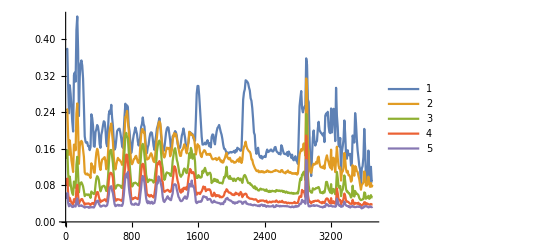

```mathematica
columns=Transpose@Rest@csv;
rounds=First[columns];
ListLinePlot[Map[Transpose[{rounds,#}]&,Rest[columns]], PlotRange->All, PlotLegends->{1,2,3,4,5}]
```

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
p1
```

{NumericArray[…]}

```mathematica
p1 = Table[Block[{len=Max[3,10]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],1];
p2 = Table[Block[{len=Max[3,10]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],1];
```

```mathematica
interpolate[p1_,p2_]:= Block[{m={}},Table[AppendTo[m,(1.0-n)*p1+n*p2],{n,0,1,0.1}]]
```

```mathematica
interpolate[Normal@p1,Normal@p2];
```

```mathematica
Dimensions@%
```

{11}

```mathematica
p1;
```

```mathematica
p2
```

{NumericArray[…]}

```mathematica
interpolate[p1_,p2_]:=Table[(1.0-n)*p1+n*p2,{n,0,1,0.05}]
NumericArray[First[#],"Real32"]&/@interpolate[Normal@p1,Normal@p2]
```

{NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…]}

```mathematica
companiesNameGenerator[#1]&/@ %
```

{Bif  Iowiu,Bif  Eowiu,Bif  Eomnu,Bif  Eomnu,Bif  Eomnu,Bifr Eomnu,Bifr Eomnu,Biyp Comnu,Biyi Comnu,Biyiebocnu,Aiyiebocnu,Aiyiebocnu,Aiyiebocnu,Agyiebocnu,Agyiebocnu,Agyiebocnu,A Yiebocnu,Araiebocnu,Araiebocnb,Eraieboena,Eraieboena}

```mathematica
companiesNameGenerator@p1
```

{Bif  Iowiu}

```mathematica
companiesNameGenerator@p2
```

{Eraieboena}

```mathematica
Rasterize[#]&/@{"Bif  Iowiu","Bif  Eowiu","Bif  Eomnu","Bif  Eomnu","Bif  Eomnu","Bifr Eomnu","Bifr Eomnu","Biyp Comnu","Biyi Comnu","Biyiebocnu","Aiyiebocnu","Aiyiebocnu","Aiyiebocnu","Agyiebocnu","Agyiebocnu","Agyiebocnu","A Yiebocnu","Araiebocnu","Araiebocnb","Eraieboena","Eraieboena"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[%]
```

```mathematica
Export["interpolation.gif",%]
```

interpolation.gif